```mathematica
SetDirectory[NotebookDirectory[]]
pblue=Lighter[Blue];
pyellow=Lighter[Yellow];
pred=Lighter[Red];
pgreen=Lighter[Green];
cf=Piecewise[{{Blend[{pred,pblue},(#+Pi)/(Pi/2)],#≤-Pi/2},{Blend[{pblue,pgreen},(#+Pi/2)/(Pi/2)],#≤0},{Blend[{pgreen,pyellow},(#)/(Pi/2)],#≤Pi/2},{Blend[{pyellow,pred},(#-Pi/2)/(Pi/2)],#≤Pi}}]&;
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@Options[g,PlotRange],Sequence@@Options[g,Epilog]]
phase[l:{_?NumericQ..}]:=Module[{args=Arg[l]},args+Prepend[2Pi Accumulate@-IntegerPart@Differences[args/Pi],0]]
nmax=10;
getphase[sig_]:=Module[{asig,plst,S1,slst1,f1},
asig=Fourier[ReplacePart[InverseFourier[sig-Mean[sig]],Join[{{1}},{#}&/@(Floor[Length[sig]/2]+Range[Floor[Length[sig]/2]])]->0]];
plst=phase[asig];
S1[n_]:=Sum[Exp[-I*n*plst[[i]]], {i,1,Length[plst]}]/Length[plst];
slst1=Table[S1[n]/(I*n),{n,1,nmax}];
f1[θ_]:=θ+Evaluate[Sum[2*Re[slst1][[n]]*(Cos[n*θ]-1)-2*Im[slst1][[n]]*Sin[n*θ],{n,1,nmax}]];
f1/@plst]
```

/Users/zack/Documents/oscillators/snakingoscillators

#### Single trajectory runs

-Graphics- | -Graphics- | -Graphics-

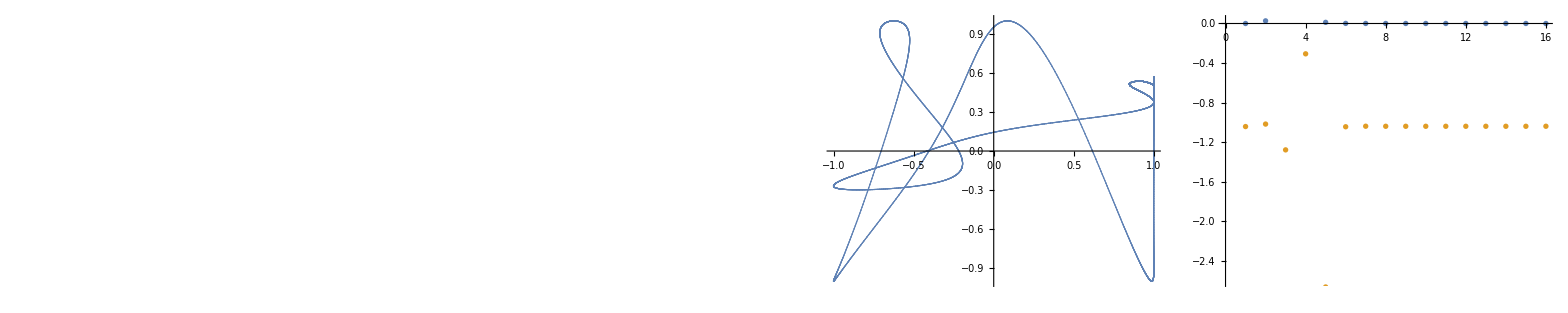

{1503,0.773609,61.1148}

```mathematica
filebase="data/chimeras/41";
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
orders=BinaryReadList[filebase<>"order.npy","Real64"][[17;;-1]];
Grid[{{rasterizeBackground[ListDensityPlot[theta[[1;;1000]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;1000]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[orders,ImageSize->300]]}}]

phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(#-#[[1]]&/@phases);
norms=Norm[#-dphases[[-1]]]&/@dphases;
mins=First/@Position[Differences[Sign[Differences[norms]]],u_/;u>0];
periods=Differences[Cases[mins,u_/;norms[[u]]<1]];
If[Length[periods]>0,
period=Round[Mean[periods]];
Grid[{{rasterizeBackground[ListDensityPlot[theta[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;period]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]]
If[Length[periods]>0,{period,Mean[orders[[-period;;-1]]],Norm[Differences[dphases[[-period+1;;-1]]],2]}]
```

#### Chimeras from random initial conditions

```mathematica
vals={#[[1]],#[[2]],#[[3]]/300,#[[4]]/100}&/@SortBy[Import["random.dat"],Norm[#[[2;;4]]]&];
dorder=0.01;
dperiod=0.01;
dnorm=0.25;
{bins,array}=HistogramList[vals[[All,2;;4]],{{dorder*(Range[1/dorder]-1)},{dperiod*(Range[3/dperiod]-1)},{0.1+dnorm*(Range[2/dnorm]-1)}}];
uniq=Table[{i,j,k}=case;
First@Cases[vals,u_/;u[[2]]>=bins[[1,i]]&&u[[2]]<=bins[[1,i+1]]&&u[[3]]>=bins[[2,j]]&&u[[3]]<=bins[[2,j+1]]&&u[[4]]>=bins[[3,k]]&&u[[4]]<=bins[[3,k+1]]],{case,(First/@ArrayRules[array])[[1;;-2]]}];
Length[uniq]
SortBy[{#[[1]],#[[2]],#[[3]]*300,#[[4]]*100}&/@uniq,{#[[2]],#[[3]],#[[4]]}&]

If[!DirectoryQ["data/chimeras"],CreateDirectory["data/chimeras"]]
seeds=uniq[[All,1]];
Length[seeds]
Do[CopyFile["data/random/"<>ToString[seeds[[i]]]<>"fs.npy","data/chimeras/"<>ToString[i]<>"ic.npy",OverwriteTarget->True], {i,1,Length[seeds]}]
```

41

{{93,0.151249,148.392,61.289},{217,0.265035,148.392,70.6404},{444,0.269731,148.627,99.8012},{701,0.304285,139.85,61.0873},{401,0.355893,469.261,145.457},{18,0.416211,822.845,175.689},{180,0.417365,296.956,116.754},{60,0.417375,296.953,105.995},{596,0.423199,150.331,79.299},{793,0.429596,218.024,94.8767},{682,0.429627,200.231,93.7311},{633,0.431166,148.645,78.1827},{382,0.431175,148.645,93.884},{143,0.467339,301.691,106.192},{812,0.46834,296.963,93.4931},{785,0.470832,299.55,79.445},{387,0.492707,148.392,50.0722},{245,0.50652,301.669,93.0974},{213,0.506523,301.669,79.0525},{148,0.507692,296.994,79.0262},{340,0.507703,296.994,93.1762},{658,0.509228,139.85,35.7477},{868,0.51679,81.76,53.9298},{638,0.516808,148.647,70.5602},{214,0.516825,148.647,93.4792},{582,0.516829,192.367,80.1036},{169,0.533197,564.675,84.9731},{683,0.533198,301.156,61.2977},{26,0.534699,296.813,61.2418},{647,0.546694,283.562,35.5584},{39,0.546706,283.562,60.8684},{782,0.548147,281.235,60.8677},{849,0.548153,281.235,35.5846},{296,0.593554,150.326,61.09},{893,0.602226,148.65,61.1114},{59,0.678674,150.328,49.9866},{154,0.680314,150.326,49.8897},{457,0.687491,148.698,69.7304},{578,0.687503,148.697,48.7535},{317,0.773606,150.326,35.248},{383,0.773609,150.326,61.1116}}

41

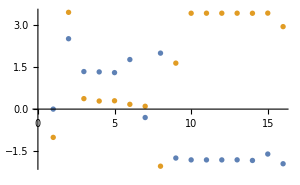
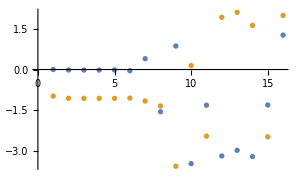
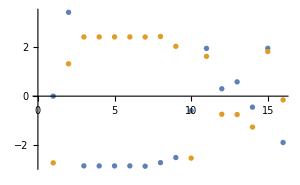
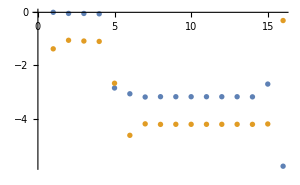
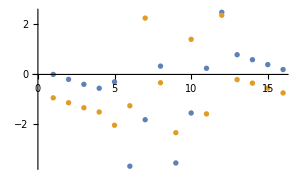
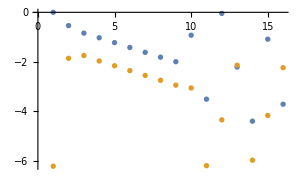
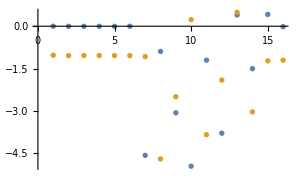
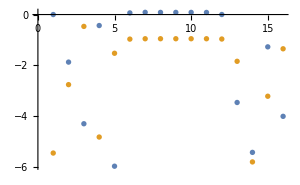
1 | 0.15124 | 148.391 | 61.2876 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
2 | 0.265045 | 148.391 | 70.6428 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
3 | 0.269759 | 318.486 | 146.342 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
4 | 0.304284 | 139.85 | 61.0868 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
6 | 0.417378 | 551.486 | 138.179 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
7 | 0.417365 | 318.164 | 120.923 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
12 | 0.431181 | 148.647 | 78.9475 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
13 | 0.43117 | 262.312 | 123.924 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
14 | 0.468341 | 296.96 | 94.077 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
16 | 0.470828 | 299.547 | 79.4477 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
17 | 0.4927 | 148.391 | 50.0741 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
18 | 0.509228 | 139.85 | 35.7464 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
19 | 0.50771 | 296.993 | 79.0224 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
20 | 0.507712 | 296.993 | 93.1788 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
21 | 0.506509 | 301.667 | 79.0565 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
22 | 0.506513 | 301.667 | 93.0617 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
24 | 0.516826 | 966.225 | 130.36 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
26 | 0.516826 | 966.225 | 129.76 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
27 | 0.534699 | 296.813 | 61.2426 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
28 | 0.533192 | 301.153 | 61.2978 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
29 | 0.533192 | 301.153 | 61.6683 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
30 | 0.548151 | 281.237 | 35.5845 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
31 | 0.548149 | 281.237 | 60.8673 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
32 | 0.546702 | 283.563 | 35.5583 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
33 | 0.546699 | 283.563 | 60.8669 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
34 | 0.593564 | 171.804 | 65.9633 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
35 | 0.602225 | 148.65 | 61.1104 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
36 | 0.678644 | 150.328 | 49.9857 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
37 | 0.687502 | 148.697 | 49.966 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
38 | 0.68749 | 148.697 | 70.585 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
39 | 0.680312 | 150.328 | 49.8886 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
40 | 0.773606 | 150.328 | 35.248 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
41 | 0.773609 | 150.328 | 61.1123 | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Monitor[p=Grid[DeleteCases[Table[filebase="data/chimeras/"<>ToString[j];
{seed,order,period,norm}=Import[filebase<>"out.dat"][[-1]];
dat=BinaryReadList[filebase<>"phases.npy","Real64"][[17;;-1]];
M=16;
theta=ArcTan[Partition[dat,4*M][[All,1;;M]],Partition[dat,4*M][[All,M+1;;2*M]]];
phi=ArcTan[Partition[dat,4*M][[All,2*M+1;;3*M]],Partition[dat,4*M][[All,3*M+1;;4*M]]];
phases=Transpose[Catenate[{Transpose[theta],Transpose[phi]}]];
dphases=(#-#[[1]]&/@phases);
If[period>0,
{Grid[{{j,order,period,norm,rasterizeBackground[ListDensityPlot[theta[[1;;Round[period/0.1];;10]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListDensityPlot[phi[[1;;Round[period/0.1];;10]],AspectRatio->1,InterpolationOrder->0,ImageSize->300,PlotRange->All,ColorFunction->cf,ColorFunctionScaling->False]],rasterizeBackground[ListPlot[Transpose[{Cos[dphases[[All,2]]],Cos[dphases[[All,M+1]]]}],PlotRange->{{-1,1},{-1,1}},ImageSize->300]],ListPlot[{dphases[[-1,1;;M]],dphases[[-1,M+1;;-1]]},ImageSize->300]}}]}],{j,1,Length[uniq]}],Null]],j]
```

#### Plot auto results

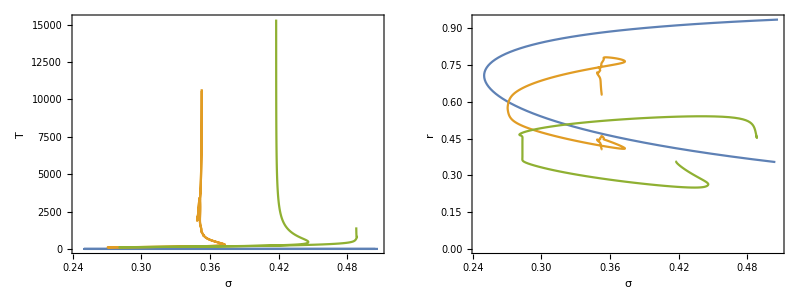

```mathematica
Grid[{{ListPlot[{Import["auto/rel/janus_rels.dat"][[1;;-2,{1,7}]],Import["auto/rel/janus_rel1.dat"][[1;;-2,{1,7}]],Import["auto/rel/janus_rel2.dat"][[1;;-2,{1,7}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1],ListPlot[{Import["auto/rel/janus_rels.dat"][[1;;-2,{1,8}]],Import["auto/rel/janus_rel1.dat"][[1;;-2,{1,8}]],Import["auto/rel/janus_rel2.dat"][[1;;-2,{1,8}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1]}}]
```

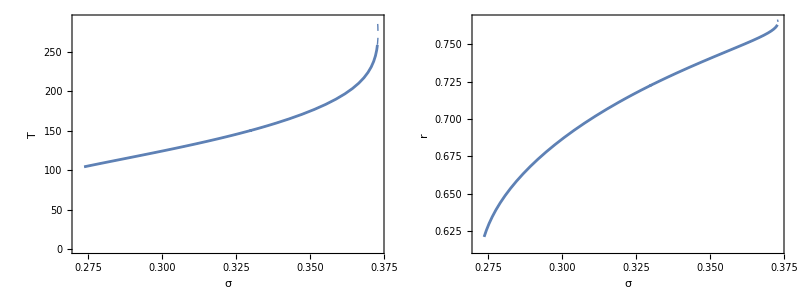

```mathematica
Grid[{{ListPlot[{DeleteCases[Import["auto/rel/40.dat"],{}][[All,{1,3}]],DeleteCases[DeleteCases[Import["auto/rel/40.dat"],{}],u_/;u[[5]]<62][[All,{1,3}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,T},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->{Directive[Dashed,AbsoluteThickness[1],ColorData[97,"ColorList"][[1]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]]}],ListPlot[{DeleteCases[Import["auto/rel/40.dat"],{}][[All,{1,4}]],DeleteCases[DeleteCases[Import["auto/rel/40.dat"],{}],u_/;u[[5]]<62][[All,{1,4}]]},Joined->True,Axes->False,Frame->True,FrameLabel->{σ,r},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotRange->All,ImageSize->300,AspectRatio->1,PlotStyle->{Directive[Dashed,AbsoluteThickness[1],ColorData[97,"ColorList"][[1]]],Directive[AbsoluteThickness[2],ColorData[97,"ColorList"][[1]]]}]}}]
```